## Chapter 1

### Unit 1.1

#### 1.1.2

```mathematica
Block[{a1=0.008,a2=0.005,θ0=π/4,ϕ0=π/4,p,a3=0.2},p[θ_,ϕ_]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Graphics3D[{{Opacity[0.2],Sphere[{0,0,0},1]},{Arrowheads[0.03],Black,Arrow@Tube[{{0,0,0},1.2#},a1]&/@IdentityMatrix[3],Arrow@Tube[{{0,0,0},p[θ0,ϕ0]}]},
{Text["\!\(n\_"<>#1<>"\)",1.1#2,{0,-1.2}]}&@@@Thread@{{"x","y","z"},IdentityMatrix[3]},
{Text["\!\(0\)",p[0,0],{1.2,0}],Text["\!\(1\)",p[π,0],{1.2,0}],Text["\!\(+\)",p[π/2,0],{0,1.2}],Text["\!\(-\)",p[π/2,π],{0,1.2}],Text["\!\(ⅈ\)",p[π/2,π/2],{0,1.2}],Text["\!\(|ⅈ\&_⟩\)",p[π/2,-π/2],{0,1.2}],Text["\!\(|ψ⟩\)",p[θ0,ϕ0],{0,-1.2}]},
{Black,Glow[GrayLevel[0.7]],Table[Tube[p[θ,#]&/@Range[0,2π,π/32],a2],{θ,{π/2,θ0}}],Tube[{{0,0,0},-#},a2]&/@IdentityMatrix[3],Table[Tube[p[#,ϕ]&/@Range[0,π,π/32],a2],{ϕ,{ϕ0}}],Tube[{{0,0,0},p[π/2,ϕ0]},a2],Glow[Black],Tube[a3 p[#,ϕ0]&/@Range[0,θ0,θ0/10],a2],Tube[a3 p[π/2,#]&/@Range[0,ϕ0,ϕ0/10],a2]},{Text["θ",a3 p[θ0,ϕ0],{0,-1}],Text["ϕ",a3 p[π/2,ϕ0/2],{0,1}]}},Boxed->False,Lighting->"Neutral",ViewPoint->{5,2,2},ImageSize->200]]
```

-Graphics3D-

```mathematica
Block[{a1=0.008,a2=0.005,θ0=π/4,ϕ0=π/4,p,a3=0.2},p[θ_,ϕ_]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Graphics3D[{{Opacity[0.2],Sphere[{0,0,0},1]},{Arrowheads[0.03],Black,Arrow@Tube[{{0,0,0},1.2#},a1]&/@IdentityMatrix[3],Arrow@Tube[{{0,0,0},p[θ0,ϕ0]}]},
{Text["\!\(n\_"<>#1<>"\)",1.1#2,{0,-1.2}]}&@@@Thread@{{"x","y","z"},IdentityMatrix[3]},
{Text["\!\(↑\)",p[0,0],{1.2,0}],Text["\!\(↓\)",p[π,0],{1.2,0}],Text["\!\(→\)",p[π/2,0],{0,1.2}],Text["\!\(←\)",p[π/2,π],{0,1.2}],Text["\!\(ⅈ\)",p[π/2,π/2],{0,1.2}],Text["\!\(|ⅈ\&_⟩\)",p[π/2,-π/2],{0,1.2}],Text["\!\(|n,+⟩\)",p[θ0,ϕ0],{0,-1.2}]},
{Black,Glow[GrayLevel[0.7]],Table[Tube[p[θ,#]&/@Range[0,2π,π/32],a2],{θ,{π/2,θ0}}],Tube[{{0,0,0},-#},a2]&/@IdentityMatrix[3],Table[Tube[p[#,ϕ]&/@Range[0,π,π/32],a2],{ϕ,{ϕ0}}],Tube[{{0,0,0},p[π/2,ϕ0]},a2],Glow[Black],Tube[a3 p[#,ϕ0]&/@Range[0,θ0,θ0/10],a2],Tube[a3 p[π/2,#]&/@Range[0,ϕ0,ϕ0/10],a2]},{Text["θ",a3 p[θ0,ϕ0],{0,-1}],Text["ϕ",a3 p[π/2,ϕ0/2],{0,1}]}},Boxed->False,Lighting->"Neutral",ViewPoint->{5,2,2},ImageSize->200]]
```

-Graphics3D-

### Unit 1.2

#### 1.2.1

```mathematica
Block[{a=0.5,b=1,lt=0.4,h=1,l=3,z=0.5,c=1,spin},
spin[col_,n_]:=Block[{r=0.1,s=0.5},{{col,Arrowheads[0.03],Arrow[Tube[s{-0.5n,n}],0.1]},{Gray,Sphere[{0,0,0},r]}}];
Graphics3D[{Translate[{Lighter[#1,lt],EdgeForm[AbsoluteThickness[1]],Cuboid[{-a,-b,-a},{a,b,a}],{White,Text[Style[#3,18,Bold,FontFamily->"Arial Black"],{a,0,0}]}},{0,0,#2h}]&@@@{{Blue,-1,"N"},{Red,1,"S"}},
{Black,Scale[Tube[BSplineCurve[{{0,-l,0},{0,-l/2,0},{0,0,0},{0,l/2,z/2},{0,l,z}}],0.02],{1,1,#},{0,0,0}]&/@{1,-1}},
Translate[spin[Purple,{1,0,0}],{0,-0.8l,0}],Translate[spin[Blue,{0,0,1}],{0,0.7l,0.7 z}],Translate[spin[Red,{0,0,-1}],{0,0.7l,-0.7 z}],
Translate[{Glow[White],Polygon[{{-c,0,-c},{-c,0,c},{c,0,c},{c,0,-c}}]},{0,l,0}],Translate[{Black,Arrowheads[0.03],{Arrow[Tube[{{0,0,0},0.8#1},0.02]],Text["\!\("<>#2<>"\)",#1]}&@@@{{{1,0,0},"x"},{{0,1,0},"y"},{{0,0,1},"z"}}},{0,-1.5l,0}]},Boxed->False,ViewPoint->{5, -3,2},Lighting->"Neutral",ImageSize->300]]
```

-Graphics3D-

### Unit 2.3

#### 2.2.1 Angular Momentum Ladder

```mathematica
Block[{jmax=3/2,fractxt},
fractxt[x_]:=If[x∈Integers,ToString[x],If[x>=0,ToString[2x]<>"\/2","-\("<>ToString[-2x]<>"\/2\)"]];
Graphics[{Arrowheads[0.03],
{AbsoluteThickness[1],LightGray,Table[Translate[Line[{0,#}&/@{-jmax-0.2,jmax+0.2}],{j,0}],{j,0,jmax,1/2}],Table[Translate[Line[{#,0}&/@{0,jmax+0.25}],{0,m}],{m,-jmax,jmax,1/2}]},{AbsolutePointSize[8],Table[Translate[{If[j∈Integers,Blue,Red],Point[{0,0}],Text[Style[StringTemplate["\!\(|`1`,`2`⟩\)"][fractxt@j,fractxt@m],"InlineFormula"],{0,0},{-1.44,0}]},{j,m}],{j,0,jmax,1/2},{m,-j,j}]},
Table[Translate[{Translate[{Green,Arrow[{0,#}&/@{m+0.2,m+0.8}],Text["\!\(J\&^\_+\)",{0,m+0.5},{1.,0}]},{-0.02,0}],Translate[{Purple,Arrow[{0,#}&/@{m+0.8,m+0.2}],Text["\!\(J\&^\_-\)",{0,m+0.5},{-1.2,0}]},{0.02,0}]},{j,0}],{j,0,jmax,1/2},{m,-j,j-1}],
{Black,AbsoluteThickness[1],Translate[{Table[Translate[{Line[Offset[{0,#}]&/@{0,3}],Text[Style[StringTemplate["\!\(`1`\)"][fractxt@j],"InlineFormula"],{0,-0.1},{0,1}]},{j,0}],{j,0,jmax,1/2}],Arrow[{#,0}&/@{-0.05,jmax+0.2}],Text["\!\(j\)",{jmax+0.2,0},{-1.2,0}]},{0,-jmax-0.3}],
Translate[{Table[Translate[{Line[Offset[{#,0}]&/@{0,3}],Text[Style[StringTemplate["\!\(`1`\)"][fractxt@m],"InlineFormula"],{0,0},{1.5,0}]},{0,m}],{m,-jmax,jmax,1/2}],Arrow[{0,#}&/@{-jmax-0.22,jmax+0.22}],Text["\!\(m\)",{0,jmax+0.2},{0,-1}]},{-0.06,0}]},
Translate[Translate[{AbsolutePointSize[8],#1,Point[{0,0}],Text[#2,{0.06,0},{-1,0}]},{0,0.15#3}]&@@@{{Blue,"Bosons",1},{Red,"Fermions",-1}},{0.05,1.5}]},AspectRatio->0.8,ImageSize->300]]
```

-Graphics-

#### 2.3.1 Exchange Topology

```mathematica
Block[{a=0.05,b=0.015,c=0.04,path},
path[ϕ_]:=Rotate[{Blend[{Red,Purple,Blue},ϕ/π],{EdgeForm[None],Cone[{2#,1,0}&/@{c,-c},c]},Tube[Table[{Cos[θ],Sin[θ],0},{θ,0.,π,π/32}],b]},ϕ,{1,0,0},{0,0,0}];
Graphics3D[{{Opacity[0.2],EdgeForm[LightGray],Polygon[1.5{{-1,-1,0},{-1,1,0},{1,1,0},{1,-1,0}}]},{Black,Sphere[{#,0,0},a]&/@{-1,0,1}},
path[0],path[π],{Opacity[0.2],path/@(Range[1,5]π/6)},Text["\!\(a\)",{0,0,0},{0,1}],Text["\!\(b\)",{1,0,0},{0,1}]},Boxed->False,Lighting->"Neutral"]]
```

-Graphics3D-

#### 2.3.1 Braid Group

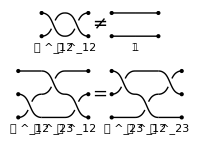

```mathematica
Block[{braid},
braid[ids_,n_]:=Block[{sigma},
sigma[i_]:=Block[{f},
f=BSplineFunction[Table[{x,Piecewise[{{0,x<0.2},{1,x>0.8}},0.5(Tanh[5(x-0.5)]+1)]},{x,0,1,0.1}]];
{Translate[Line[{#,0}&/@{0,1}],{0,#}]&/@Complement[Range[n],{i,i+1}],If[i>0,Translate[{{Line[f/@Range[0,0.4,0.02]],Line[f/@Range[0.6,1,0.02]]},Scale[Line[f/@Range[0,1,0.02]],{1,-1},{0.5,0.5}]},{0,i}]]}];{MapIndexed[Translate[{sigma[#1],Text[If[#1>0,StringTemplate["\!\(𝒫\&^\_\(`1``2`\)\)"][#1,#1+1],""],{0.5,0.5}]},{First@#2,0}]&,ids],Translate[Point[{1,#}&/@Range[n]],{#,0}]&/@{0,Length[ids]}}];
Graphics[{Translate[{Translate[braid[{1,1},2],{-3.5,0}],Text[Style["\!\(≠\)",18],{0,1.5}],Text["\!\(𝟙\)",{1.5,0.5}],Translate[braid[{-1,-1},2],{-0.5,0}]},{0,3.5}],
Translate[{Translate[braid[{1,2,1},3],{-4.5,0}],Text[Style["\!\(=\)",18],{0,2}],Translate[braid[{2,1,2},3],{-0.5,0}]},{0,0}]},PlotRangePadding->Scaled[.05],ImageSize->200]
]
```

### Unit 3.1

#### 3.1.1 Reflection

```mathematica
Block[{hf=0.05,θ=π/3},
Graphics[{{Red,AbsoluteThickness[2],Arrowheads[{{0.06,0.55}}],Arrow[ReIm@{ⅈ Exp[ⅈ θ],0}],Arrow[ReIm@{0,ⅈ Exp[-ⅈ θ]}]},{{HatchFilling[],Rectangle[{-1,0},{1,-hf}]},Line[{#,0}&/@{-1,1}]},{AbsoluteThickness[1],{Dashed,Line[ReIm@{0,0.3ⅈ}]},Circle[{0,0},0.15,{π/2,π/2+θ}],Circle[{0,0},0.14,{π/2,π/2-θ}],Circle[{0,0},0.16,{π/2,π/2-θ}],Text["\!\(θ\_i\)",ReIm[0.25 ⅈ Exp[ⅈ θ/2]]],Text["\!\(θ\_r\)",ReIm[0.25 ⅈ Exp[-ⅈ θ/2]]],Text["\!\(n\)",{1,0},{1,-1}]}},ImageSize->180]]
```

-Graphics-

#### 3.1.1 Refraction

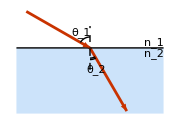

```mathematica
Block[{hf=0.05,θ1=π/3,θ2=π/6},
Graphics[{{Lighter[Blue,0.8],Rectangle[{-1,0},{1,-0.9}]},{Red,AbsoluteThickness[2],Arrowheads[{{0.06,0.55}}],Arrow[ReIm@{ⅈ Exp[ⅈ θ1],0}],Arrow[ReIm@{0,-ⅈ Exp[ⅈ θ2]}]},{Line[{#,0}&/@{-1,1}]},{AbsoluteThickness[1],{Dashed,Line[ReIm@{-0.3ⅈ,0.3ⅈ}]},Circle[{0,0},0.15,{π/2,π/2+θ1}],Circle[{0,0},0.14,-{π/2,π/2-θ2}],Circle[{0,0},0.16,-{π/2,π/2-θ2}],Text["\!\(θ\_1\)",ReIm[0.25 ⅈ Exp[ⅈ θ1/2]]],Text["\!\(θ\_2\)",ReIm[-0.3ⅈ Exp[ⅈ θ2/2]]],Text["\!\(n\_1\)",{1,0},{1,-1}],Text["\!\(n\_2\)",{1,0},{1,1}]}},ImageSize->180]]
```

#### 3.1.2 Huygens Principle

```mathematica
Block[{y0=-10,r0=10,dr=0.1,dθ=0.005π,dθ2=0.05π,θmax=0.2π,θb=0.16π,wv,wc},
wv[r_,θ_,dk_]:=Block[{col},col=Lighter[Yellow,1-dk];{EdgeForm[col],col,Polygon[ReIm[ⅈ Flatten[-y0+{r  Exp[ⅈ (θ+dθ{-1,1}/2)],(r+dr)Exp[ⅈ (θ+dθ{1,-1}/2)]}]]]}];
wc[r_,θ_,dk_]:=Table[{Opacity[Mod[a,1] dk],Yellow,Annulus[ReIm[ⅈ(-y0+r Exp[ⅈ θ])],{a-dr,a}]},{a,2-dr,2dr,-dr}];
Graphics[{Table[wv[r,θ,Mod[r,1]LogisticSigmoid[20(θb^2-θ^2)]LogisticSigmoid[0.5r Sin[θ]]],{θ,-θmax,θmax,dθ},{r,r0+3,r0+5-dr,dr}],
Block[{r=r0+3},Table[wc[r,θ,LogisticSigmoid[-0.5r Sin[θ]]],{θ,dθ2,-θmax+dθ2,-dθ2}]],
Table[wv[r,θ,Mod[r,1]LogisticSigmoid[20(θb^2-θ^2)]],{θ,-θmax,θmax,dθ},{r,r0,r0+3-dr,dr}],
Translate[{Point[{0,0}],Text["\!\(r\_0\)",{0,0},{0,1.2}]},ReIm[ⅈ(-y0+(r0+3) Exp[-ⅈ dθ2])]],Translate[{Point[{0,0}],Text["\!\(r\)",{0,0},{0,-1}]},ReIm[ⅈ(-y0+(r0+4) Exp[ⅈ (-dθ2+0.01π)])]]},ImageSize->220]]
```

-Graphics-

#### 3.1.2 Reflection

```mathematica
Block[{hf=0.05,θ=π/3,λ=0.25,d=0.4,wave,shd},
wave[n_]:=First@ContourPlot[Mod[n.{x,y},λ]LogisticSigmoid[20(d-Abs[Det[{n,{x,y}}]])],{x,-1,1},{y,0,1},Contours->32,ContourStyle->None,ExclusionsStyle->None,ColorFunction->(Directive[Opacity[#^2],Yellow]&)];
shd={{White,Table[Translate[#,0.02r],{r,CirclePoints[32]}]},#}&;
Graphics[{wave[ReIm[-ⅈ Exp[ⅈ θ]]],wave[ReIm[ⅈ Exp[-ⅈ θ]]],{{HatchFilling[],Rectangle[{-1,0},{1,-hf}]},Line[{#,0}&/@{-1,1}]},{AbsoluteThickness[1],Arrowheads[{# 0.04,(1+#)/2,Graphics[Line[Offset/@{{-3,-2},{0,0},{-3,2}}]]}&/@{-1,1}],Translate[{Circle[{0,0},0.1,{0,θ}],Text["\!\(θ\_i\)",{0.1,0},{-1,-0.8}]},{-2λ/Sin[θ],0}],Translate[{Circle[{0,0},0.1,π-{0,θ}],Text["\!\(θ\_r\)",{-0.1,0},{1,-0.8}]},{2λ/Sin[θ],0}],Translate[{Arrow[{# λ/Sin[θ],0}&/@{-0.5,0.5}],shd@Text["\!\(λ\_∥\)",{0,0},{0,0.2}]},{-0.5λ/Sin[θ],0}],
Translate[{Rotate[{Arrow[{0,# λ}&/@{-0.5,0.5}]},θ,{0,0}],Text["\!\(λ\)",{0,0},{-0.5,-0.8}]},ReIm[(1.5λ-0.5d ⅈ) ⅈ Exp[ⅈ θ]]]},Text["\!\(n\)",{1,0},{1,-1}]},ImageSize->180]]
```

-Graphics-

#### 3.1.2 Refraction

```mathematica
Block[{θ1=π/3,θ2=π/6,λ1=0.25,λ2,w1=0.4,w2=0.6,wave,shd},
λ2=λ1/Sin[θ1] Sin[θ2];
wave[n_,λ_,y0_,w_]:=First@ContourPlot[Mod[n.{x,y},λ]LogisticSigmoid[20(w-Abs[Det[{n,{x,y}}]])],{x,-1,1},{y,0,y0},Contours->32,ContourStyle->None,ExclusionsStyle->None,ColorFunction->(Directive[Opacity[#^2],Yellow]&)];
shd={{White,Table[Translate[#,0.02r],{r,CirclePoints[32]}]},#}&;
Graphics[{{Lighter[Blue,0.8],Rectangle[{-1,0},{1,-0.9}]},
wave[ReIm[-ⅈ Exp[ⅈ θ1]],λ1,0.7,w1],wave[ReIm[-ⅈ Exp[ⅈ θ2]],λ2,-0.9,w2],{Line[{#,0}&/@{-1,1}]},
{AbsoluteThickness[1],Arrowheads[{# 0.04,(1+#)/2,Graphics[Line[Offset/@{{-3,-2},{0,0},{-3,2}}]]}&/@{-1,1}],Translate[{Circle[{0,0},0.1,{0,θ1}],Text["\!\(θ\_1\)",{0.1,0},{-1,-0.8}]},{-2λ1/Sin[θ1],0}],Translate[{Circle[{0,0},0.1,π+{0,θ2}],Text["\!\(θ\_2\)",{-0.1,0},{1,0.8}]},{λ2/Sin[θ2],0}],Translate[{Arrow[{# λ1/Sin[θ1],0}&/@{-0.5,0.5}],shd@Text["\!\(λ\_∥\)",{0,0},{0,0.2}]},{-0.5λ1/Sin[θ1],0}],
Translate[{Rotate[{Arrow[{0,# λ1}&/@{-0.5,0.5}]},θ1,{0,0}],Text["\!\(λ\_1\)",{0,0},{-0.5,-0.8}]},ReIm[(1.5λ1-0.8w1 ⅈ) ⅈ Exp[ⅈ θ1]]],
Translate[{Rotate[{Arrow[{0,# λ2}&/@{-0.5,0.5}]},θ2,{0,0}],Text["\!\(λ\_2\)",{0,0},{1,0.5}]},ReIm[(-0.5λ2+0.8w2 ⅈ) ⅈ Exp[ⅈ θ2]]]},Text["\!\(n\_1\)",{1,0},{1,-1}],Text["\!\(n\_2\)",{1,0},{1,1}]},ImageSize->180]]
```

-Graphics-

### Unit 3.3

#### 3-3-2 Tunneling

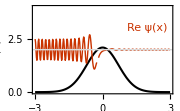

```mathematica
Block[{m=1,Ε=2,ℏ=0.05,dx=0.02,V,p,W,ψ,xmin,xmax},
V[x_]:=2.1Exp[-x^2];
p[x_]:=Sqrt[2m(Ε-V[x])];
W[x_?NumericQ]:=Quiet[NIntegrate[p[x1],{x1,-3,x}]];
ψ[x_?NumericQ]:=Exp[ⅈ W[x]/ℏ]/Sqrt[Abs[p[x]]];
{xmin,xmax}={-3,3};
Plot[V[x],{x,xmin,xmax},PlotStyle->Black,Axes->False,FrameLabel->{"\!\(x\)","\!\(V(x)\)"},Prolog->{AbsoluteThickness[1],LightGray,InfiniteLine[{#,Ε}&/@{0,1}]},Epilog->{Translate[{Red,Cases[ListLinePlot[Block[{data},data=Table[If[Abs[p[x]]dx>ℏ/10,{x,Re@ψ[x]},{x,Null}],{x,xmin,xmax,dx}];
data[[All,2]]=0.5data[[All,2]]/Abs[data[[1,2]]];data]],_Line,∞],Text["\!\(Re ψ(x)\)",{2,1},{0,0}]},{0,Ε}]},PlotRange->{0,4},PlotRangePadding->{Scaled[0.02],Scaled[0.05]},ImageSize->180]
]
```

### Unit 4.2

#### 4-2-2 AB Effect

```mathematica
Block[{sol,gauge,traj},
sol=Block[{lt=0.9},{{EdgeForm[Black],Lighter[Green,lt],Disk[]},{Green,Point[Cases[Tuples[Range[-1,1,0.4],2],p_/;Norm[p]<1]]},{{{Lighter[Green,lt],Table[Translate[#,r],{r,0.08CirclePoints[24]}]},{Green,#}}&@Text["\!\(B\)",{0,0}]}}];
gauge:=Block[{a=0.2,b=0.5,rs},
rs=Table[Piecewise[{{Exp[1/2(2x-1)],x>1/2},{Sqrt[2x],True}}],{x,a,2,0.5}];{Red,Arrowheads[{0.01,#,Graphics[{Line[Offset/@{{-5,3},{0,0},{-5,-3}}]}]}&/@{0,0.5}],Table[Arrow[ReIm[r Exp[ⅈ (b Log[r]+Range[0,2π,π/32])]]],{r,rs}],Text["\!\(A\)",{1.5,0.4}]}];
traj={Blue,{Arrowheads[{{0.06,0.53}}],AbsoluteThickness[2],Scale[Arrow[BSplineCurve[Block[{h1=0.15,h2=2.6},{{-5,0},{-4.9,h1},{-2,h2},{2,h2},{4.9,h1},{5,0}}]]],{1,#},{0,0}]&/@{1,-1}},{Text["\!\(𝒞\_lower\)",{0,-2.4},{0,1}],Text["\!\(𝒞\_upper\)",{0,2.4},{0,-1.1}]},Translate[Block[{a=0.2},{Disk[{0,0},a],AbsoluteThickness[1],Table[Line[ReIm[{1.6,2.2}a Exp[ⅈ θ]]],{θ,π/6,2π,π/6}],Text["source",{0,-0.8},{0,1}]}],{-5,0}],Translate[Block[{h=0.8,α=0.3},{Line[{0,#}&/@{-h,h}],AbsoluteThickness[1],Table[Line[{{0,y},{α h/2,y-α h/2}}],{y,-h+α h,h,α h}],Text["screen",{0,-0.8},{0,1}]}],{5,0}]};
Graphics[{sol,gauge,traj},ImageSize->220]]
```

-Graphics-

#### 4-2-3 SQUID

```mathematica
Block[{h=0.1,r1=0.75,r2=1,w=0.1,l=1.5,f=1,a=0.01,ring,junct,flux},ring=First@RegionPlot3D[RegionDifference[RegionUnion[#1,Cuboid[{-l,-w,-w},{l,w,w}]],#2]&@@(Cylinder[{0,0,#}&/@{-h,h},#]&/@{r2,r1}),PlotPoints->32,MaxRecursion->2,Mesh->None,PlotStyle->LightBlue];
junct=First@RegionPlot3D[RegionIntersection[RegionDifference@@(Cylinder[{0,0,#}&/@{-h,h},#]&/@{r2,r1}),Cuboid[{-w,-1,-1},{w,1,1}]],PlotPoints->32,MaxRecursion->2,Mesh->None,PlotStyle->Blue];
flux[r_,θ_]:={Arrow@Tube[Table[{r Sqrt[1+z^2]Cos[θ],r Sqrt[1+z^2]Sin[θ],z},{z,-f,f,0.1f}],a]};
Graphics3D[{ring, junct,{Blue,Text[Style["Josephson\njunction",LineSpacing->{0,14}],{0,-r1,-w},{0,1.6}]},{Black,Arrowheads[0.03],flux[0.5,2π#/6]&/@Range[6],Text["flux \!\(Φ\)",{0.1,0.1,f}]},{Translate[{{White,Arrow[{#,0,0}&/@{-0.15,0.2}]},{Black,Text["Current",{0,0,0},{-0.5#,1.5},{1,-0.1}]}},{# (1+(l-1)/2),-w,0}]&/@{-1,1}}},Boxed->False,ViewPoint->{0.5, -2.4, 2.},ImageSize->240]
]
```

-Graphics3D-